```mathematica
Graphs = SortBy[Import["/Users/alexanderhabib/Desktop/PDG_UGR/Graphs/connected_graphs/n_7/graph7c.g6","Graph6"],EdgeCount];
AList = AdjacencyMatrix[#]&/@Graphs;
```

```mathematica
PrimePiProx[num_]:= If[num<2,0,N[LogIntegral[num]-LogIntegral[2]]]
CountPrimes[A_,d_]:=Module[{P,max, min,SampleCount, PrimeCount, ProbOfPrime,Prob},
P =MatrixPower[A,#]&/@Range[2,d];
P = DeleteCases[Join[Statistics`Library`UpperTriangularMatrixToVector[#],Normal[Diagonal[#]]],0]&/@P;
max = Max[#]+1&/@P ;
min =Min[#]&/@P ;
PrimeCount = Length[Select[#,PrimeQ]]&/@P;
SampleCount = Length[P[[1]]];
(*ProbOfPrime = N[(PrimePiProx/@(max) - PrimePiProx/@(min-1))/(max-min+ 1)];
Prob = PDF[BinomialDistribution[SampleCount,ProbOfPrime[[#]]],PrimeCount[[#]]]&/@Range[Length[P]];*)
max-min
]
```

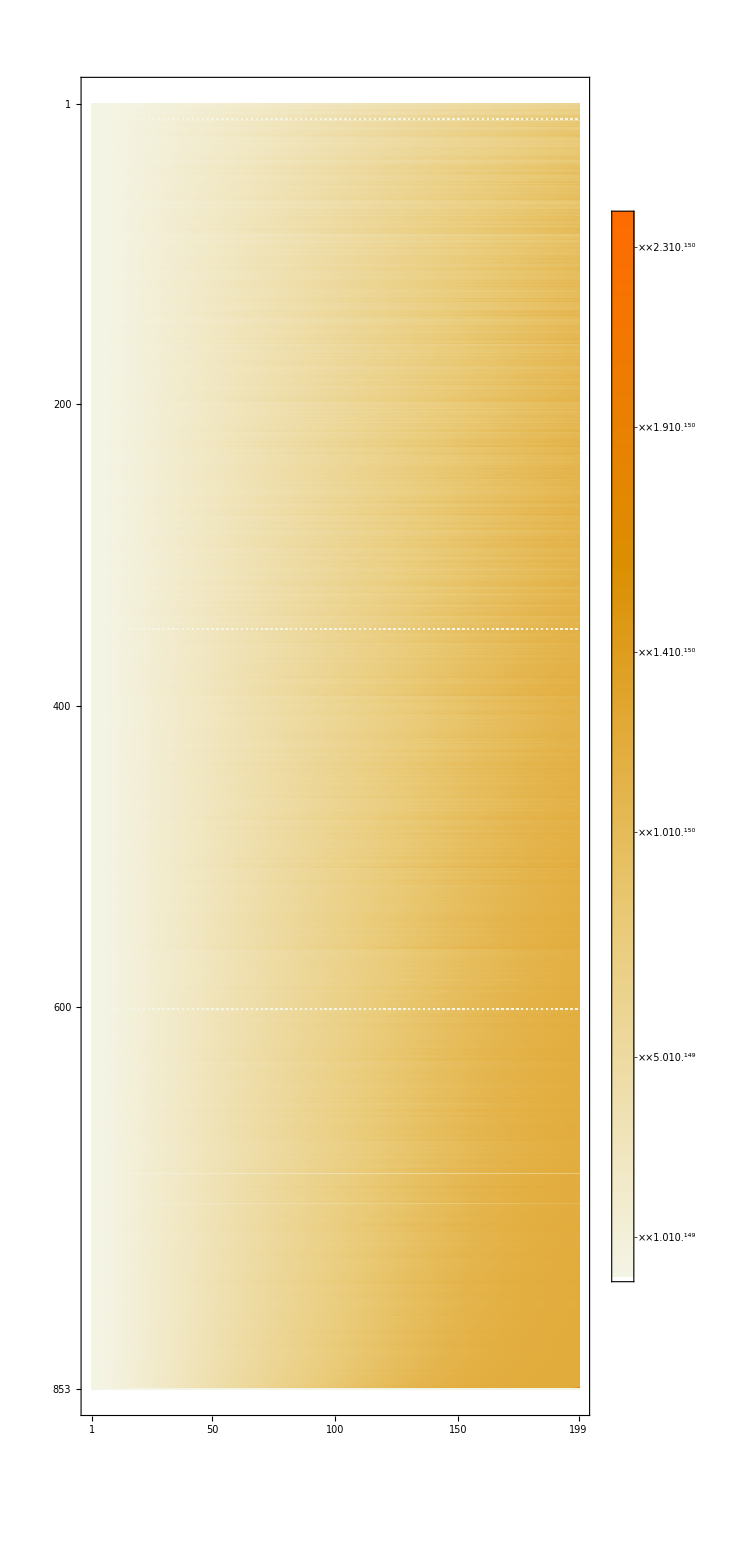

-Graphics-

```mathematica
k=200;
Temp =CountPrimes[#,k]&/@AList[[;;-1]];
MatrixPlot[Temp,PlotLegends->Automatic]
Histogram[Mean/@Temp]
```

```mathematica
Length[Graphs]
```

853

```mathematica
Temp2 = SortBy[{AList[[#]],Temp[[#]]}&/@Range[Length[Temp]],Total[#[[2]]]&];
```

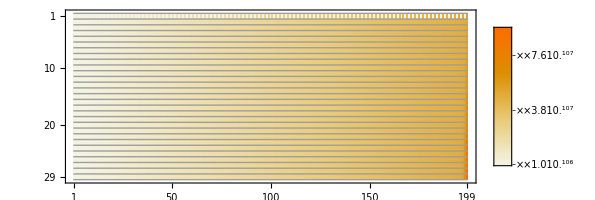

```mathematica
MatrixPlot[Temp2[[422;;450,2]],PlotLegends->Automatic,Mesh->{All,None},MaxPlotPoints->Infinity]
```

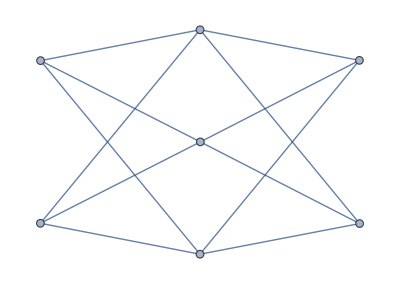

```mathematica
AdjacencyGraph@Temp2[[422,1]]
```